## example script for generating asymmetric samples [David Kipping, Columbia University]

```mathematica
"Suppose you want to draw samples from x=μ_-σneg^(+σpos), where xmin<x<xmax";
xmin=-∞;xmax=∞;
μ=1;σneg=0.1;σpos=0.3;
```

```mathematica
TraditionalForm["x=μ_-σneg^(+σpos) ∈ (xmin,xmax)"]
```

x=μ_-σneg^(+σpos) ∈ (xmin,xmax)

```mathematica
"define a mixture distribution";
dist=MixtureDistribution[{PDF[NormalDistribution[μ,σneg],μ],PDF[NormalDistribution[μ,σpos],μ]},{TruncatedDistribution[{μ,xmax},NormalDistribution[μ,σpos]],TruncatedDistribution[{xmin,μ},NormalDistribution[μ,σneg]]}];
```

```mathematica
TraditionalForm[PDF[dist,x]]
```

Piecewise[{{ⅇ^(-(x-μ)^2/(2 σneg^2))/(2 π σneg σpos (1/(√(2 π) σneg)+1/(√(2 π) σpos)) (1/2-1/2 erfc((μ-xmin)/(√2 σneg)))), x-xmin>0∧x-μ≤0}, {ⅇ^(-(x-μ)^2/(2 σpos^2))/(2 π σneg σpos (1/(√(2 π) σneg)+1/(√(2 π) σpos)) (1/2 erfc((μ-xmax)/(√2 σpos))-1/2)), x-μ>0∧x-xmax≤0}}]

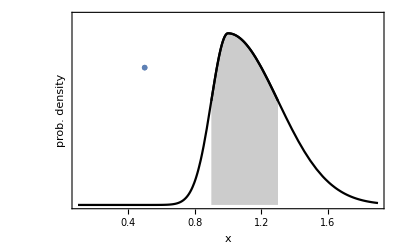

```mathematica
"plot the PDF";
pdfplot=Show[Plot[PDF[dist,x],{x,μ-σneg,μ},Axes->None,Frame->True,PlotStyle->Black,Filling->Axis,FrameLabel->{"x","prob. density"},FrameTicks->{Automatic,None},PlotRange->{{μ-3Max[σneg,σpos],μ+3Max[σneg,σpos]},{0,1.1PDF[dist,μ]}},BaseStyle->{FontFamily->"CMU Serif"}],Plot[PDF[dist,x],{x,μ,μ+σpos},Axes->None,Frame->True,PlotStyle->Black,Filling->Axis,PlotRange->{{μ-3Max[σneg,σpos],μ+3Max[σneg,σpos]},{0,1.1PDF[dist,μ]}}],Plot[PDF[dist,x],{x,μ-3Max[σneg,σpos],μ+3Max[σneg,σpos]},Axes->None,Frame->True,PlotStyle->Black],ListPlot[{{0.5,0.8PDF[dist,μ]}},PlotMarkers->Style["x=1_-0.1^(+0.3)",Black,FontSize->22]]]
```

```mathematica
"check it has the expected 1-sigma credible interval";
Integrate[PDF[dist,x],{x,μ-σneg,μ+σpos}]
N[Erf[1/√2]]
```

0.682689

0.682689

```mathematica
"draw samples";
samples=RandomVariate[dist,10^6];
```

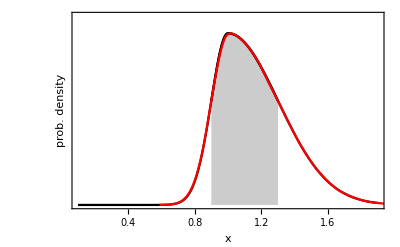

```mathematica
"compare to PDF";
Show[pdfplot,SmoothHistogram[samples,PlotStyle->Red]]
```